## PBIL

λ - wspolczynnik uczenia sie, size-liczebnosc populacji, n-wymiar

```mathematica
Clear[pbil,newP,valuate,compare];
(*funkcja zliczająca ilość jedynek w osobniku*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*funkcja zwracająca osobnika z większą liczbą jedynek*)
compare[x_,y_]:=If[valuate[x]>valuate[y],x,y];
(*PBIL dyskretny  n-długość osobnika, λ-parametr uczący się, size- liczność populacji*)
pbil[n_,λ_,size_]:=Module[{P=Table[0.5,{n}],best,population=Table[Table[0,{n}],{size}], iter=1,wynik=Table[{0,0},{1}]},
(*generacja pop startowej wedug prawdopodobieństwa 1/2 *)
SeedRandom[];
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];
best=population⟦1⟧;

(*Algorytm kończy się po znalezieniu najlepszego*)
While[valuate[best]!=n  ,
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compare[population⟦i⟧,best]
];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,valuate[best]};

(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n,i++,P[[i]]=(1-λ)*P[[i]]+λ*best[[i]];]

(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];

iter++;
wynik2=Table[{iter,valuate[best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];
Print["Wektor jednostkowy uzyskany po iteracjach: ",iter];
Print[best];
ListPlot[wynik]
]
```

### λ=0.2 (wpada w jedna wartosc i nie zmienia sie od pierwszej iteracji)

```mathematica
pbil[8,0.2,12] (* wysoki λ- ustalenie się prawdopodobienstwa, brak zmian w kolejnych populacjach*)
```

$Aborted

### λ=0.01

Wektor jednostkowy uzyskany po iteracjach: 30

{1,1,1,1,1,1,1,1}

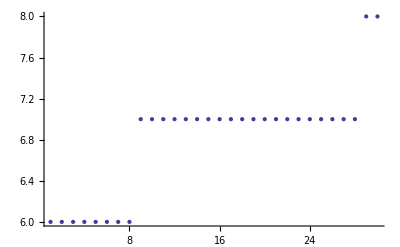

```mathematica
pbil[8,0.01,12]
```

### λ=0.001

best:{1,1,1,0,1,1,0,1} iter: 1

best:{1,1,1,0,1,1,1,1} iter: 2

best:{1,1,1,0,1,1,1,1} iter: 3

best:{1,1,1,0,1,1,1,1} iter: 4

best:{1,1,1,0,1,1,1,1} iter: 5

best:{1,1,1,1,1,1,1,1} iter: 6

Wektor jednostkowy uzyskany po iteracjach: 7

{1,1,1,1,1,1,1,1}

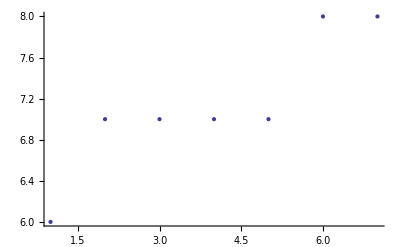

```mathematica
pbil[8,0.001,12]
```

### λ=0.0001

```mathematica
pbil[8,0.0001,12]
```

best:{1,0,1,1,0,1,0,1} iter: 1

best:{1,1,0,1,1,1,1,1} iter: 2

best:{1,1,0,1,1,1,1,1} iter: 3

best:{1,1,0,1,1,1,1,1} iter: 4

best:{1,1,0,1,1,1,1,1} iter: 5

best:{1,1,0,1,1,1,1,1} iter: 6

best:{1,1,0,1,1,1,1,1} iter: 7

best:{1,1,1,1,1,1,1,1} iter: 8

Wektor jednostkowy uzyskany po iteracjach: 9

{1,1,1,1,1,1,1,1}

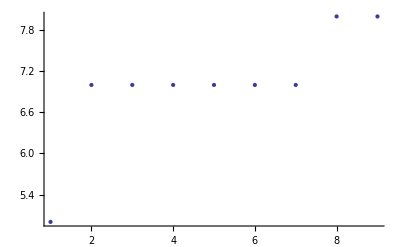

Wniosek : Szybsze rezultaty są osiągane dla niższych współczynników uczenia się.

## PBIL 2

```mathematica
Clear[pbil,newP,valuate,compare];
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
pbil2[n_,λ_,f_,size_,max_,itmax_]:=Module[{P=Table[0.5,{n}],best,population=Table[Table[0,{n}],{size}], iter=1,wynik=Table[{0,0},{1}]},
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników*)
compare[x_,y_]:=If[f[x]>f[y],x,y];
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
(*Print[population];*)
(*Print["best:",best];*)

(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
While[(f[best]≠max  && iter≠itmax),
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compare[population⟦i⟧,best]];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,f[best]};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n,i++,P[[i]]=(1-λ)*P[[i]]+λ*best[[i]];]
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];

iter++;
wynik2=Table[{iter,f[best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];
(*Print["Maximum (",max,") uzyskane po iteracjach: ",iter-1];
Print[best];
Print[wynik];*)
(*ListLinePlot[wynik];*)
Return[{iter-1,max-f[best]}]
]
```

#### trap

```mathematica
trap[k_,x_]:= If[valuate[x]<k,k-1-valuate[x],k]
```

trap_k(u)=Piecewise[{{k-1 - u,, u<k}, {k,, inaczej}}]
trap_5(u)=Piecewise[{{4- u,, u<5}, {k,, inaczej}}]

trap5 λ=0.001

```mathematica
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
```

```mathematica
trap7[x_]:=trap[7,x];
pbil2[5,0.001,trap5,20,5,100]
```

{5,0}

```mathematica
λ=0.5;n=7;max=n;
iter=0;val=0;
Print["λ ="+λ];
Do[rez=pbil2[n,λ,trap7,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.]
```

0.5+λ =

5:{63.61,1.84}

20:{15.71,0.41}

50:{2.81,0.03}

100:{1.43,0.}

200:{1.16,0.}

```mathematica
λ=0.2;os=50;n=7;max=n;
iter=0;val=0;
Print["λ ="+λ];
Do[rez=pbil2[n,λ,trap7,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.]
```

0.2+λ =

5:{34.72,0.92}

20:{4.,0.03}

50:{2.06,0.}

100:{1.42,0.}

200:{1.26,0.}

```mathematica
λ=0.1;os=50;n=7;max=n;
iter=0;val=0;
Print["λ ="+λ];
Do[rez=pbil2[n,λ,trap7,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.]
```

0.1+λ =

5:{19.53,0.39}

20:{3.76,0.}

50:{2.18,0.}

100:{1.44,0.}

200:{1.19,0.}

```mathematica
λ=0.01;os=50;n=7;max=n;
iter=0;val=0;
Print["λ ="+λ];
Do[rez=pbil2[n,λ,trap7,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.]
```

0.01+λ =

5:{14.99,0.}

20:{5.61,0.}

50:{2.59,0.}

100:{1.65,0.}

200:{1.26,0.}

```mathematica
λ=0.0001;os=50;n=7;max=n;
iter=0;val=0;
Print["λ ="+λ];
Do[rez=pbil2[n,λ,trap7,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap7,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.]
```

0.0001+λ =

5:{25.91,0.02}

20:{7.89,0.}

50:{3.08,0.}

100:{1.76,0.}

200:{1.2,0.}

```mathematica
(*trap 10 tests*)
```

```mathematica
λ=0.5;n=10;max=n;
iter=0;val=0;
Print["λ =",λ];
Do[rez=pbil2[n,λ,trap10,5,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,20,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,50,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,100,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,200,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,500,max,150];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["500:",{iter,val}/100.]
```

λ =0.5

5:{141.76,3.6}

20:{84.58,1.97}

50:{37.64,0.77}

100:{7.94,0.12}

200:{4.78,0.06}

500:{1.66,0.}

```mathematica
λ=0.2;n=10;max=n;
iter=0;val=0;
Print["λ =",λ];
Do[rez=pbil2[n,λ,trap10,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,500,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["500:",{iter,val}/100.]
```

λ =0.2

5:{71.36,2.59}

20:{30.72,0.92}

50:{7.78,0.12}

100:{2.86,0.}

200:{2.22,0.}

500:{1.79,0.}

```mathematica
λ=0.1;n=10;max=n;
iter=0;val=0;
Print["λ =",λ];
Do[rez=pbil2[n,λ,trap10,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,500,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["500:",{iter,val}/100.]
```

λ =0.1

5:{56.79,1.8}

20:{12.78,0.18}

50:{4.79,0.}

100:{3.85,0.}

200:{2.79,0.}

500:{1.69,0.}

```mathematica
λ=0.01;n=10;max=n;
iter=0;val=0;
Print["λ =",λ];
Do[rez=pbil2[n,λ,trap10,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,500,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["500:",{iter,val}/100.]
```

λ =0.01

5:{42.21,0.06}

20:{20.21,0.}

50:{12.49,0.}

100:{7.42,0.}

200:{4.7,0.}

500:{2.16,0.}

```mathematica
λ=0.0001;n=10;max=n;
iter=0;val=0;
Print["λ =",λ];
Do[rez=pbil2[n,λ,trap10,5,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["5:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,20,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["20:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,50,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["50:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,100,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["100:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,200,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["200:",{iter,val}/100.];iter=0;val=0;
Do[rez=pbil2[n,λ,trap10,500,max,100];val+=rez⟦2⟧;iter+=rez⟦1⟧,{100}];Print["500:",{iter,val}/100.]
```

λ =0.0001

5:{78.45,0.97}

20:{40.79,0.13}

50:{21.14,0.01}

100:{10.82,0.}

200:{4.88,0.}

500:{2.28,0.}

trap5 λ=0.1

{{0,1,1,0,0},{0,1,0,1,1},{0,1,1,0,0},{1,1,0,0,1},{0,0,1,1,0},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,1,0},{1,0,0,0,0},{0,1,0,0,0},{1,0,1,0,1},{0,0,1,1,0},{0,0,1,0,0},{1,0,1,0,0},{0,1,1,0,1},{0,0,0,0,1},{1,1,1,1,1},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1}}

Maximum (5) uzyskane po iteracjach: 1

{1,1,1,1,1}

{{1,5},{2,5}}

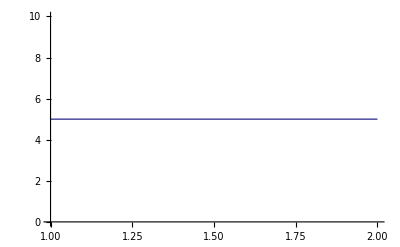

```mathematica
pbil2[5,0.01,trap5,20,5,100]
```

trap6 λ=0.2

```mathematica
trap6[x_]:=trap[6,x];
```

Maximum (6) uzyskane po iteracjach: 0

{0,1,1,1,0,1}

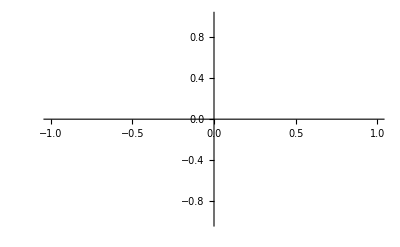

```mathematica
pbil2[6,0.02,trap6,20,6,100]
```

trap6 λ=0.2 populacja 20os

{{1,0,0,0,0,0},{1,1,1,1,0,1},{1,0,1,0,1,0},{1,0,1,1,0,1},{1,1,0,0,1,0},{1,0,1,0,0,0},{0,1,0,1,1,1},{1,0,0,1,0,1},{0,1,1,1,1,1},{0,1,1,0,0,0},{1,0,0,0,1,0},{0,1,1,0,1,1},{1,1,1,1,0,0},{1,1,0,0,1,1},{1,1,0,0,1,0},{0,0,0,0,1,1},{0,0,1,1,0,0},{1,1,0,0,1,1},{0,1,0,1,1,0},{1,0,1,0,1,1}}

Maximum (6) uzyskane po iteracjach: 5

{1,1,1,1,1,1}

{{1,3},{2,3},{3,3},{4,3},{5,6},{6,6}}

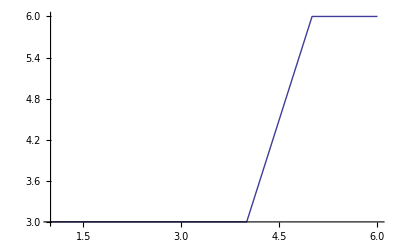

```mathematica
pbil2[6,0.02,trap6,20,6,100]
```

trap6 λ=0.2 populacja 5os

```mathematica
pbil2[6,0.02,trap6,5,6,100]
```

Maximum (6) uzyskane po iteracjach: 0

{0,1,0,1,1,1}

-Graphics-

trap6 λ=0.00001

{{1,1,0,0,0,1},{1,0,1,1,1,1},{1,0,1,1,0,1},{1,0,0,0,0,0},{1,1,1,1,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,1,1,1,0,0},{1,1,1,0,1,0},{1,0,0,1,0,1},{1,1,1,0,0,0},{1,0,0,0,0,1},{0,1,0,0,1,0},{0,0,0,1,0,0},{1,0,0,1,1,1},{0,0,0,0,0,1},{1,0,0,1,1,1},{0,0,0,0,0,1},{1,1,0,1,0,1},{0,1,1,1,0,0}}

Maximum (6) uzyskane po iteracjach: 3

{1,1,1,1,1,1}

{{1,3},{2,4},{3,6},{4,6}}

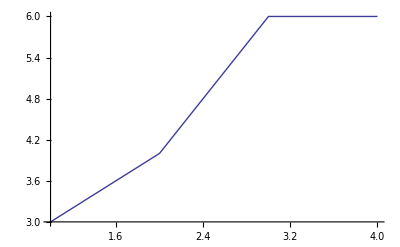

```mathematica
pbil2[6,0.00001,trap6,20,6,100]
```

### valuate dla λ=0.001, 10 bit, 20 osobnikow, max 100iteracji

{{0,0,1,1,1,0,1,1,0,1},{0,1,0,0,1,1,1,0,1,0},{0,1,0,0,1,1,0,1,0,1},{1,0,1,1,0,1,0,0,1,1},{1,1,0,1,1,0,1,1,1,0},{1,0,1,1,1,1,1,1,1,1},{0,1,1,0,1,0,0,1,1,1},{1,0,0,1,0,1,0,1,1,0},{1,0,1,0,0,1,1,0,0,1},{0,0,1,1,0,0,0,1,1,0},{0,1,0,0,1,0,0,1,1,0},{1,1,1,1,0,0,1,0,1,0},{0,0,0,1,0,1,1,1,1,0},{1,1,0,1,1,0,0,0,0,0},{1,0,1,0,0,0,1,1,0,1},{1,1,0,0,0,0,0,0,1,0},{1,1,0,0,0,1,0,0,1,0},{0,0,1,1,0,1,1,0,0,0},{1,1,0,1,1,1,1,1,0,1},{1,0,0,0,0,0,0,1,1,1}}

Maximum (10) uzyskane po iteracjach: 12

{1,1,1,1,1,1,1,1,1,1}

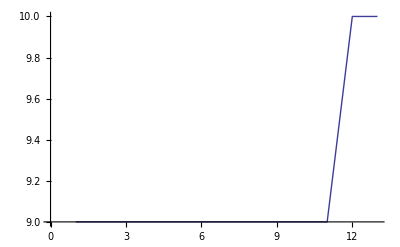

```mathematica
pbil2[10,0.001,valuate,20,10,100]
```

### 3deceptive

f_(3deceptive)(u)=Piecewise[{{0.9, u=0}, {0.8, u=1}, {0, u=2}, {1, inaczej}}]

```mathematica
f3d[x_]:=Module[{q=valuate[x]},
If[q==0,0.9,
If[q==1,0.8,
If[q==2,0,1]]]];
```

```mathematica
f3d[{0,0,0,0,1}]
```

0.8

```mathematica
3-deceptive testy
```

```mathematica
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
```

dł osobnika = 3

```mathematica
λa={.5,.2,.1,.01,.0001};osa={5,20,50,100,200,500};max=1;n=3;
For[qq=1,qq<6,qq++,
Print["λ = ",λa⟦qq⟧];
For[je=1,je<7,je++,
λ=λa⟦qq⟧;os=osa⟦je⟧;val=0;iter=0;
Do[rez=pbil2[n,λ,f3d,os,max,100];
iter+=rez[[1]];val+=rez[[2]];
,{100}];
Print["pop = ",os," : ",{iter,val}/100.];
];
Print["___________________"]
]
```

λ = 0.5

pop = 5 : {6.42,0.01}

pop = 20 : {0.92,0.}

pop = 50 : {0.9,0.}

pop = 100 : {0.82,0.}

pop = 200 : {0.86,0.}

pop = 500 : {0.91,0.}

___________________

λ = 0.2

pop = 5 : {1.69,0.}

pop = 20 : {0.95,0.}

pop = 50 : {0.86,0.}

pop = 100 : {0.85,0.}

pop = 200 : {0.85,0.}

pop = 500 : {0.86,0.}

___________________

λ = 0.1

pop = 5 : {1.7,0.}

pop = 20 : {0.91,0.}

pop = 50 : {0.9,0.}

pop = 100 : {0.9,0.}

pop = 200 : {0.85,0.}

pop = 500 : {0.82,0.}

___________________

λ = 0.01

pop = 5 : {1.75,0.}

pop = 20 : {0.97,0.}

pop = 50 : {0.86,0.}

pop = 100 : {0.88,0.}

pop = 200 : {0.86,0.}

pop = 500 : {0.93,0.}

___________________

λ = 0.0001

pop = 5 : {2.04,0.}

pop = 20 : {1.05,0.}

pop = 50 : {0.93,0.}

pop = 100 : {0.92,0.}

pop = 200 : {0.84,0.}

pop = 500 : {0.89,0.}

___________________

dł. osobnika = 5

```mathematica
λa={.5,.2,.1,.01,.0001};osa={5,20,50,100,200,500};max=1;n=10;
For[qq=1,qq<6,qq++,
Print["λ = ",λa⟦qq⟧];
For[je=1,je<7,je++,
λ=λa⟦qq⟧;os=osa⟦je⟧;val=0;iter=0;
Do[rez=pbil2[n,λ,f3d,os,max,100];
iter+=rez[[1]];val+=rez[[2]];
,{100}];
Print["pop = ",os," : ",{iter,val}/100.];
];
Print["___________________"]
]
```

λ = 0.5

pop = 5 : {0.02,0.}

pop = 20 : {0.03,0.}

pop = 50 : {0.05,0.}

pop = 100 : {0.07,0.}

pop = 200 : {0.06,0.}

pop = 500 : {0.03,0.}

___________________

λ = 0.2

pop = 5 : {0.07,0.}

pop = 20 : {0.05,0.}

pop = 50 : {0.02,0.}

pop = 100 : {0.02,0.}

pop = 200 : {0.04,0.}

pop = 500 : {0.06,0.}

___________________

λ = 0.1

pop = 5 : {0.05,0.}

pop = 20 : {0.06,0.}

pop = 50 : {0.08,0.}

pop = 100 : {0.,0.}

pop = 200 : {0.07,0.}

pop = 500 : {0.06,0.}

___________________

λ = 0.01

pop = 5 : {0.1,0.}

pop = 20 : {0.07,0.}

pop = 50 : {0.02,0.}

pop = 100 : {0.03,0.}

pop = 200 : {0.08,0.}

pop = 500 : {0.04,0.}

___________________

λ = 0.0001

pop = 5 : {0.04,0.}

pop = 20 : {0.05,0.}

pop = 50 : {0.07,0.}

pop = 100 : {0.1,0.}

pop = 200 : {0.02,0.}

pop = 500 : {0.04,0.}

___________________

```mathematica
rez
```

{4,0}

3 deceptive λ=0.2

{{0,0,1,1,0},{0,0,1,1,1},{0,1,0,1,1},{1,1,1,1,0},{1,1,1,0,0},{1,1,0,1,0},{1,0,1,0,0},{0,1,0,0,1},{1,1,0,1,1},{1,0,1,0,0},{0,1,1,0,1},{0,0,0,1,0},{1,0,1,0,0},{0,1,0,0,0},{0,0,1,1,1},{1,1,0,0,1},{1,0,0,0,0},{1,0,0,1,1},{0,0,0,0,0},{0,1,0,0,1}}

Maximum (1) uzyskane po iteracjach: 1

{0,0,1,1,1}

{{1,1},{2,1}}

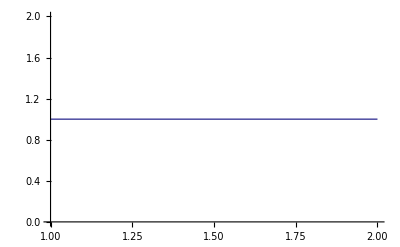

```mathematica
pbil2[5,0.001,f3d,20,1,100]
```

3 deceptive λ=0.001, 3-bit

```mathematica
pbil2[3,0.001,f3d,20,1,100]
```

{{0,1,0},{1,0,1},{1,0,0},{1,1,1},{0,1,0},{1,0,0},{1,1,1},{0,0,1},{0,1,1},{0,1,1},{0,0,1},{0,0,1},{1,0,0},{1,1,1},{1,1,1},{1,0,1},{0,0,0},{0,0,1},{0,0,0},{0,0,0}}

Maximum (1) uzyskane po iteracjach: 1

{1,1,1}

{{1,1},{2,1}}

-Graphics-

3 deceptive λ=0.5 4-bit

```mathematica
pbil2[4,0.5,f3d,20,1,100]
```

{{0,1,0,1},{0,1,0,1},{1,0,0,0},{1,0,1,1},{0,1,0,0},{1,1,0,1},{1,1,1,0},{0,0,1,1},{1,0,0,1},{1,0,1,1},{0,0,0,1},{0,0,1,0},{0,0,0,0},{1,0,1,0},{0,1,1,1},{1,0,0,0},{0,0,1,0},{0,1,1,0},{1,1,0,1},{1,0,0,0}}

Maximum (1) uzyskane po iteracjach: 1

{1,0,1,1}

{{1,1},{2,1}}

-Graphics-

3 deceptive λ=0.5 4-bit populacja 5

{{1,1,0,1},{1,1,1,1},{0,0,0,1},{0,1,1,0},{1,1,0,0}}

Maximum (10) uzyskane po iteracjach: 99

{1,1,0,1}

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{36,1},{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{50,1},{51,1},{52,1},{53,1},{54,1},{55,1},{56,1},{57,1},{58,1},{59,1},{60,1},{61,1},{62,1},{63,1},{64,1},{65,1},{66,1},{67,1},{68,1},{69,1},{70,1},{71,1},{72,1},{73,1},{74,1},{75,1},{76,1},{77,1},{78,1},{79,1},{80,1},{81,1},{82,1},{83,1},{84,1},{85,1},{86,1},{87,1},{88,1},{89,1},{90,1},{91,1},{92,1},{93,1},{94,1},{95,1},{96,1},{97,1},{98,1},{99,1},{100,1}}

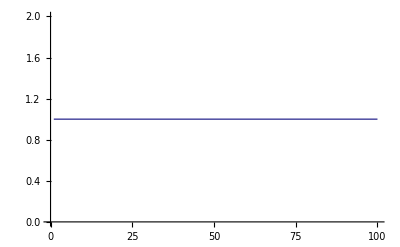

```mathematica
pbil2[4,0.5,f3d,5,10,100]
```

Wniosek : Nie znaleziono ekstremum, zbyt wysoki wsp. uczenia się

Max diversity
Z=∑_(i=1)^(n-1) ∑_(j=i+1)^n d_ij x_ix_j, gdzie dodatkowo ∑_(i=1)^n x_i=m, d_ij= (∑_(k=1)^r (s_ik-s_jk)^2)^(1/2)

```mathematica
d[i_,j_,x_]:=√(∑_(k=1)^Length[x] (x⟦i⟧-x⟦j⟧)^2);
(*X-wszystkie osobniki,konkretny osonik, w którym wartość liczymy*)
MD[x_]:=∑_(i=1)^(Length[x]-1) ∑_(j=i+1)^Length[x] d[i,j,x] x⟦i⟧ x⟦j⟧;
```

```mathematica
MD[{{1,0,1},{0,0,1},{1,1,1}},{0,1,1}]
```

MD[{{1,0,1},{0,0,1},{1,1,1}},{0,1,1}]

## PBIL 3 (dla max diversity)

```mathematica
Clear[pbil3,newP,valuate,compare];
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x]},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*Losuje osobnika z m jedynkami*)
osobnik[p_,n_,m_]:=Module[{x=Table[0,{n}]},
SeedRandom[];
While[valuate[x]!=m, 
For[i=1,i<=n,i++,
x⟦i⟧=RandomChoice[{p,1-p}->{0,1}];
];
];x

];
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
(*dodatkowo zakładamy, że w osobniku jest m jedynek*)
pbil3[n_,λ_,f_,m_,size_,max_,itmax_]:=Module[{P=Table[0.5,{n}],best,population=Table[Table[0,{n}],{size}], iter=1,wynik=Table[{0,0},{1}]},
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników*)
compare[x_,y_]:=If[f[x]>f[y],x,y];
(*Zainicjowanie populacji, by spelnione bylo zalozenie valuate[x]=m*)
For[i=1,i≤size,i++,
For[j=1,j≤m,j++,
population[[i,j]]=1]];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
While[((*f[best]≠max  &&*) iter≠itmax),
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compare[population⟦i⟧,best]];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,f[best]};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i<=n,i++,P⟦i⟧=(1-λ) P⟦i⟧+λ best⟦i⟧;]
(*Generacja nowej populacji*)
For[j=1,j<=size,j++,
For[i=1,i<=n,i++,
(*population⟦j,i⟧=1*)osobnik[P⟦i⟧,n,m]
]];
iter++;
wynik2=Table[{iter,f[best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];
Print["Maximum (",max,") uzyskane po iteracjach: ",iter-1];
Print[best];
(*Print[wynik];*)
ListLinePlot[wynik]
]
```

3max diversity λ=0.5 6-bit populacja 5

```mathematica
(*dł osobnika, współczynnik uczenia się, f-funkcja optymalizowana, il jedynek w osobniku, rozmiar populacji, rzeczywiste maximum funkcji, ilość iteracji która kończy algorytm*)
```

Maximum (1) uzyskane po iteracjach: 7

{1,1,1,0,0,0}

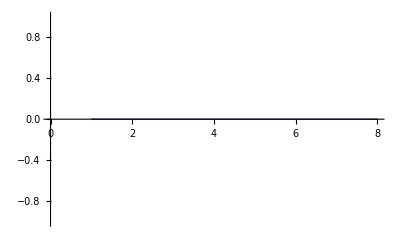

```mathematica
pbil3[6,.5,MD,3,5,1,8]
```